```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Legendre wavelet definition*)
$k=5; $M=3;
LegendrePn[l_,x_]:=Sqrt[l+1/2]LegendreP[l,x]
nhat[n_]:=2n-1
wavelet[n_,l_,x_]:=If[(nhat[n]-1)/2^($k)≤x≤ (nhat[n]+1)/2^($k),2^($k/2)LegendrePn[l,2^($k)x-nhat[n]],0]
```

```mathematica
import[file_String]:=Total/@(Import[file,"Data"]/.{a_,b_String,c_String}:> {a,StringJoin[b,c]//StringReplace[#,{"e-"~~x_:> "*10^(-"~~x~~")","im"-> "*I"}]&//ToExpression})
```

```mathematica
mu$10$data=Import["data/output/NLO_wavelet_coeff_mu_10.0.txt","Data"]//Flatten//Partition[#,2^($k-1)*$M]&;
quark$10GeV[x_]:=Sum[wavelet[n,m,x]*mu$10$data[[1]][[n+m*2^($k-1)]],{n,1,2^($k-1)},{m,0,$M-1}];
gluon$10GeV[x_]:=Sum[wavelet[n,m,x]*mu$10$data[[2]][[n+m*2^($k-1)]],{n,1,2^($k-1)},{m,0,$M-1}];
```

```mathematica
mu$1000$data=Import["data/output/NLO_wavelet_coeff_mu_1000.0.txt","Data"]//Flatten//Partition[#,2^($k-1)*$M]&;
quark$1000GeV[x_]:=Sum[wavelet[n,m,x]*mu$1000$data[[1]][[n+m*2^($k-1)]],{n,1,2^($k-1)},{m,0,$M-1}];
gluon$1000GeV[x_]:=Sum[wavelet[n,m,x]*mu$1000$data[[2]][[n+m*2^($k-1)]],{n,1,2^($k-1)},{m,0,$M-1}];
```

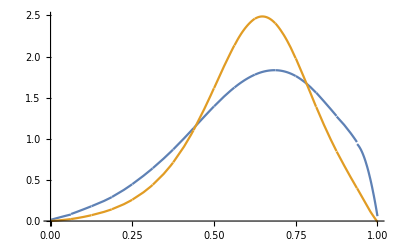

```mathematica
Plot[{quark$10GeV[x],quark$1000GeV[x]},{x,0,1}]
```

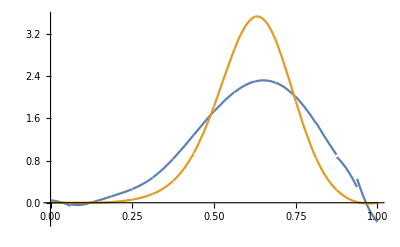

```mathematica
Plot[{gluon$10GeV[x],gluon$1000GeV[x]},{x,0,1}]
```